```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
white=Graphics[{White,Rectangle[{0,0},{256,256}]},ImageSize->256]
```

-Graphics-

```mathematica
Export["white.png",white];
```

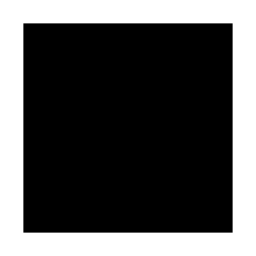

```mathematica
black=
```

```mathematica
Export["white.png",Graphics[{White,Rectangle[]},ImageSize->64]]
```

white.png

```mathematica
Table[Export[ToString[t - 5]<>".png",Graphics[{Hue[0.35,t/20.0,1-t/20.0],Rectangle[{0,0},{256,256}]},ImageSize->64]],{t,0,20,1}]
```

{-5.png,-4.png,-3.png,-2.png,-1.png,0.png,1.png,2.png,3.png,4.png,5.png,6.png,7.png,8.png,9.png,10.png,11.png,12.png,13.png,14.png,15.png}